```mathematica
probabilityToHit = 0.25
```

0.25

```mathematica
single = probabilityToHit*0.5;
double = probabilityToHit*0.25;
triple = probabilityToHit*0.125;
homerun = probabilityToHit*0.125;
single+double+triple + homerun
```

0.25

This could help us determine the optimal batting order given hitting probability / profile.
Can help us determine the expected distributions of scores - number of “blow outs” number of “shut outs”.
What if we changed to 4 or 2 outs per inning?
Calculate expected men stranded.  Men stranded in scoring position.
What if one team hits x% better than the other - what is the winning percentage of each team?

```mathematica
batterUp[{0,0,0, 0}, 2, 0.5]
```

{{0,0,0,0},3}

```mathematica
single+double+triple + homerun
```

0.25

```mathematica
batterUp[runners_, outs_, mult_]
```

```mathematica
batterUp[{0,0,0,0},0, 0.5]
```

{0,0,0,0}

0.2186

{{0,0,0,0},1}

```mathematica
batterUp[runners_, outs_, mult_]:=Module[{},
 (* value = Random[]; *)
value = 0.2186;
out=If[value > 0.25*mult, outs + 1, outs];
newrunners = Which[
value <= mult*single, hit[runners], 
mult*(single+double)>=value >mult*single, permuteRunners[ hit[runners]],
mult*(single+double+triple)>=value >mult*(single+double),permuteRunners[permuteRunners[ hit[runners]]],
mult*(single+double+triple + homerun)>=value >(single+double+triple),permuteRunners[permuteRunners[permuteRunners[ hit[runners]]]],
value > mult*(single+double+triple + homerun), runners];
Print[newrunners];
Print[value];
{newrunners, out}]
```

```mathematica
playInning[runs_, mult_, totalouts_]:=Module[{},
runners={0,0,0, runs};
outs=0;
While[outs<totalouts,
{runners, outs}=batterUp[runners, outs, mult];];
runners[[4]]]
```

```mathematica
assessSeason[season_]:=N[(Length[Select[season, #[[1]]==#[[2]]&]]/2 + Length[Select[season, #[[1]]>#[[2]]&]])/Length[season]]
```

```mathematica
hit[ runners_]:=Module[{},
newrunners={1, runners[[1]], runners[[2]], runners[[3]]+runners[[4]]};
newrunners]
```

```mathematica
permuteRunners[ runners_]:=Module[{},
newrunners={0, runners[[1]], runners[[2]], runners[[3]]+runners[[4]]};
newrunners]
```

```mathematica
computeWinning[team_, opponent_, years_]:=Module[{},
guys = {};
For[teams = 1, teams < years,
season={};
For[games= 1, games<= 162, 
runs=0;
runsOpponent=0;
For[i=1, i<=9,
runs=playInning[runs, team, 3];
runsOpponent=playInning[runsOpponent, opponent, 3];
i++];
season=Append[season,{runs, runsOpponent}];
games++];
guys = Append[guys,assessSeason[season]];
teams++];
guys]
```

```mathematica
(* Distribution of WP for even teams *)
```

```mathematica
results=computeWinning[1, 1, 300];
```

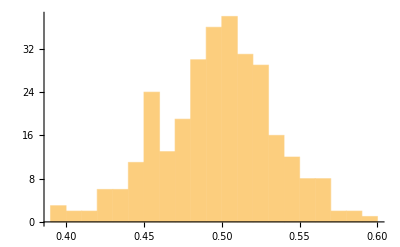

```mathematica
Histogram[results, 20]
```

```mathematica
results=computeWinning[1.1, 1, 300];
```

```mathematica
StandardDeviation[results]
```

0.0374762

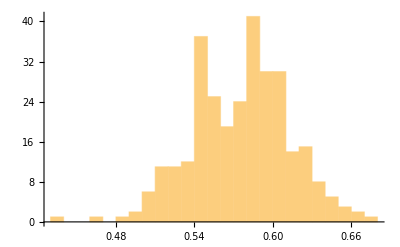

```mathematica
Histogram[results, 20]
```

```mathematica
Mean[results]
```

0.575302

```mathematica
For[ba=0, ba<10,
season={};
For[games= 1, games<= 162, 
runs=0;
For[i=1, i<=9,
runs=playInning[runs,1.1, 3];
i++];
season=Append[season,runs];
games++];
ba++]
```

```mathematica
season
```

{7,3,5,9,3,5,1,2,1,1,3,1,3,5,5,2,3,2,1,6,4,0,5,1,5,2,4,3,7,2,7,2,5,4,10,5,6,2,2,4,2,3,3,5,1,2,6,2,4,4,4,1,3,4,9,4,4,5,5,1,1,2,2,1,2,5,2,2,0,1,4,1,3,2,2,3,6,0,2,4,2,9,0,3,6,2,2,5,7,0,3,1,1,6,3,4,1,3,5,3,2,2,3,3,1,0,2,1,0,1,7,2,3,3,0,1,3,0,4,0,1,2,2,3,0,6,1,1,0,0,3,2,4,2,5,2,4,5,6,3,3,3,1,4,2,5,0,2,2,3,3,2,4,9,2,2,3,4,7,15,3,3}

```mathematica
result={};
For[ba= 1, ba<6,
season={};
For[games= 1, games<= 162, 
runs=0;
For[i=1, i<=9,
runs=playInning[runs, 1, ba];
i++];
season=Append[season,runs];
games++];
result=Append[result,{ba,  N[Mean[season]]}]; 
ba++]
```

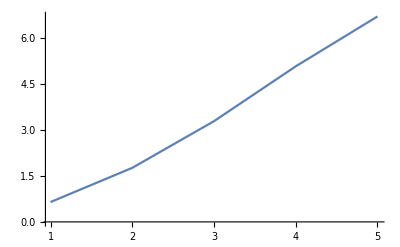

```mathematica
ListPlot[result, Joined->True]
```

```mathematica
runs=0;
For[i=1, i<=9,
Print[i];
Print[runs];
runs=playInning[runs, 0.9, 3];
i++];
```

1

0

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

Null

0.2186

```mathematica
playInning[0, 0.1, 3]
```

0

```mathematica
rr
```

```mathematica
playInning[0, 0.5, 3]
```

0

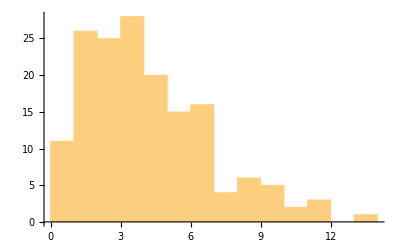

```mathematica
Histogram[#[[1]]&/@season, 20]
```

```mathematica
N[Mean[#[[1]]&/@season]]
```

3.69136

```mathematica
Length[Select[season, #[[1]]==#[[2]]&]]
```

19